## 0) Preliminaries

```mathematica
plotFun[fun_,lims_,epilog_,label_]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{Full,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]
```

```mathematica
discPlotFun[fun_,range_,lims_,epilog_,label_]:=Framed@DiscretePlot[fun,{x,range[[1]],range[[2]]},PlotRange->lims,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"k","y"},BaseStyle->{FontSize->20}]
```

## 1) Verknüpfung

```mathematica
P(G)×P(G)->P(G)
(A,B)↦A⋆B
A⋆B:={a·b|a∈A,b∈B}={g∈G|∃a∈A,∃b∈B:g=a·b}
```

Associativity

```mathematica
We need to prove that A⋆(B⋆C)==(A⋆B)⋆C. Suppose we have x∈A⋆(B⋆C). It is equivalent to the statement: x=a·g, where a∈A and g∈B⋆C. That is x=a·(b·c)  for some a∈A,b∈B,c∈C. We know that a·(b·c)=(a·b)·c, so x=(a·b)·c and thus x∈(A⋆B)⋆C. We proved A⋆(B⋆C)⊂(A⋆B)⋆C. The proof for (A⋆B)⋆C⊂A⋆(B⋆C) is analogous.
```

Neutral element

```mathematica
Let the neutral element be E={e}. Then A⋆E={a·e|a∈A}={a|a∈A}=A. And E⋆A={e·a|a∈A}={a|a∈A}=A. And thus A⋆E=E⋆A=A.
```

## 2) Körper

```mathematica
∀a,b∈𝕂:(-a)·b==-(a·b)
```

```mathematica
A=ℚ+√2 ℚ={a+√2 b|a,b∈ℚ} ←Körper?
```

Useful formulas:

Inverse element for addition

(∀x∈𝕂)(∃x̄∈𝕂)(x+x̄=x̄+x=0)

Notation:x̄=-x

Distributivity

∀x,y,z∈𝕂: (x+y)·z = x·z+y·z

Inverse element

```mathematica
(a·b)+(-a)·b==0 (definition of inverse element)
```

```mathematica
a·b+(-a)·b==0
```

```mathematica
(a+(-a))·b==0(distributive law)
```

```mathematica
0·b==0(definition of inverse element)
```

```mathematica
Validity of the previous equality follows from Satz 1.4 in Skript.
```

Field (Körper) with rational numbers

Close for addition and multiplication?

```mathematica
(Subscript[a, 1]+√2 Subscript[b, 1])+(Subscript[a, 2]+√2 Subscript[b, 2])=(Subscript[a, 1]+Subscript[a, 2])+√2(Subscript[b, 1]+Subscript[b, 2])∈ℚ+√2 ℚ
```

```mathematica
(Subscript[a, 1]+√2 Subscript[b, 1])·(Subscript[a, 2]+√2 Subscript[b, 2])=(Subscript[a, 1] Subscript[a, 2]+2 Subscript[b, 1] Subscript[b, 2])+√2(Subscript[a, 1] Subscript[b, 2]+Subscript[b, 1] Subscript[a, 2])∈ℚ+√2 ℚ
```

Associative?

```mathematica
As in ℝ...
```

Commutative?

```mathematica
As in ℝ...
```

Distributive?

```mathematica
As in ℝ...
```

Exist neutral elements?

```mathematica
neutral element for addition:OverBar[0]:=(0+√2·0)∈ℚ+√2 ℚ
```

```mathematica
neutral element for multiplication:OverBar[1]:= (1+√2·0)∈ℚ+√2 ℚ
```

Exists inverse element for addition?

```mathematica
(a+√2 b)+((-a)+√2(-b))=(a+(-a))+√2(b+(-b))=0+√2·0=OverBar[0]
```

Exists inverse element for multiplication?

```mathematica
(a+√2 b)·(ā+√2 b̄)=1+√2·0=OverBar[1]
```

```mathematica
(a ā+2b b̄)+√2(a b̄+b ā)  ⇒ a ā+2b b̄=1 ∧  a b̄+b ā=0
```

```mathematica
a b̄+b ā=0 ⇒ā:=a k ∧ b̄:=-b k
```

```mathematica
a ā+2b b̄=1 ⇒a (a k)+2b (-b k)=1 ⇒ (a^2-2 b^2)k=1
```

```mathematica
a^2-2 b^2≠0?
```

```mathematica
a≠±√2 b ← Yes, because a/b∈ℚ, but √2∉ℚ.
```

```mathematica
We therefore have k=1/(a^2-2 b^2) and finally we can conclude, that the multiplicative inverse element for a+√2 b is:
```

```mathematica
ā+√2 b̄, where ā:=a/(a^2-2 b^2)and b̄:=-b/(a^2-2 b^2)
```

## 3) Schnittpunkt zweier Geraden

```mathematica
Subscript[G, v,t]=={v+λ·t|λ∈ℝ}
v,t∈ℝ^2
```

```mathematica
v=({{0}, {1}}), t=({{-1}, {2}}), w=({{1}, {2}}), s=({{1}, {-1}})
```

```mathematica
Subscript[G, v,t]∩Subscript[G, w,s]=?
```

Calculation

```mathematica
Subscript[G, v,t]={({{-λ}, {1+2λ}})|λ∈ℝ}
```

```mathematica
Subscript[G, w,s]={({{1+λ}, {2-λ}})|λ∈ℝ}
```

```mathematica
Subscript[G, v,t]∩Subscript[G, w,s]={({{a}, {b}})∈ℝ^2|∃Subscript[λ, 1],Subscript[λ, 2]∈ℝ: ({{a}, {b}})=({{-Subscript[λ, 1]}, {1+2 Subscript[λ, 1]}})=({{1+Subscript[λ, 2]}, {2-Subscript[λ, 2]}})}
```

```mathematica
-Subscript[λ, 1]=1+Subscript[λ, 2] ∧ 1+2 Subscript[λ, 1]=2-Subscript[λ, 2]
```

```mathematica
Solution for Subscript[λ, 1],Subscript[λ, 2]: Subscript[λ, 1]=2,Subscript[λ, 2]=-3
```

```mathematica
Intersection point:({{a}, {b}})= ({{-(2)}, {1+2(2)}})=({{-2}, {5}})
```

Graphically

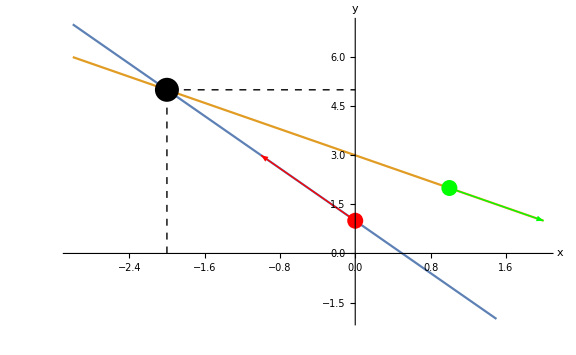

```mathematica
plotFun[{1-2x,3-x},{{-3,2},{-2,7}},{{PointSize[.03],Dashed,Line[{{-2,0},{-2,5},{0,5}}],Point[{-2,5}]},{Red,PointSize[.02],Point[{0,1}],Arrow[{{0,1},{0,1}+{-1,2}}]},{Green,PointSize[.02],Point[{1,2}],Arrow[{{1,2},{1,2}+{1,-1}}]}},""]
```